2

142586

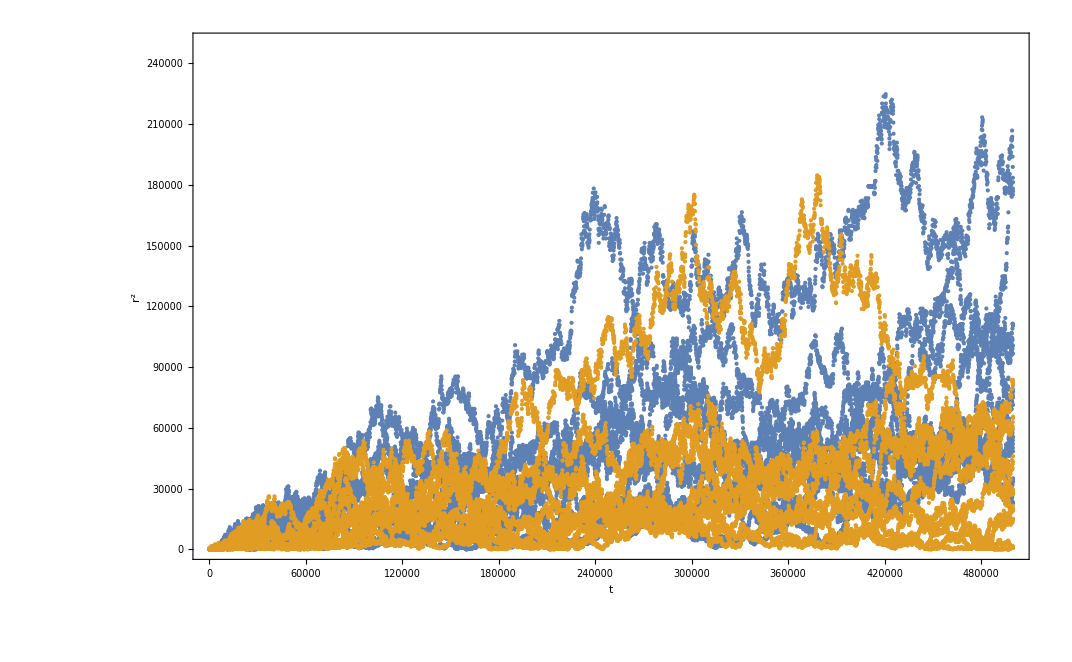

```mathematica
s="D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\Alone_L1000OT500000_u30t1.txt";
data=ReadList[s,{Number,Number,Number}];
T=50000;
z=Floor[(Length@data)/T]
Length[data]
t=Table[Take[data,{T(i-1)+1,T*i}],{i,1,z}];
r=Table[{t[[i,j,1]],t[[i,j,2]]^2+t[[i,j,3]]^2},{i,1,z},{j,1,T}];
ListPlot[r,Frame->True,FrameLabel->{"t","r^2"},PlotRange->{0,500^2}]
```

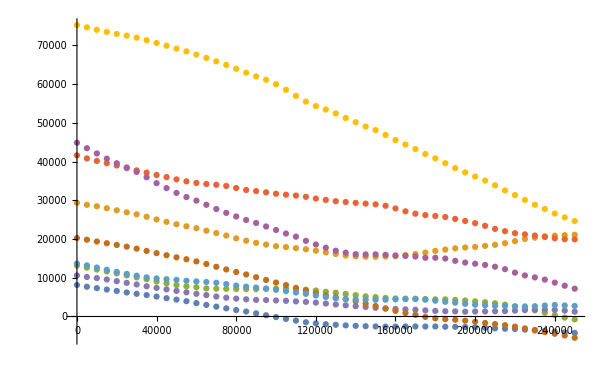

```mathematica
ListPlot[Table[{10h,1/(T-h)Sum[t[[k,j,2]]*t[[k,j+h,2]]+t[[k,j,3]]*t[[k,j+h,3]],{j,1,T-h}]},{k,1,z},{h,0,T/2,500}]]
```

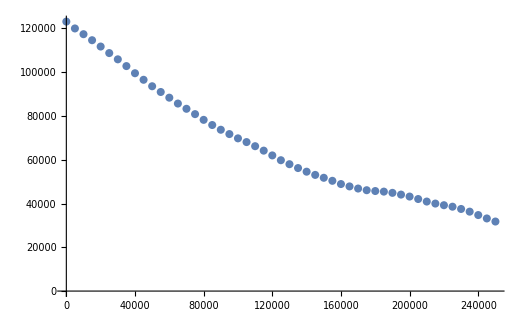

```mathematica
ListPlot[Table[{10h,1/(T-h)Sum[t[[k,j,2]]*t[[k,j+h,2]]+t[[k,j,3]]*t[[k,j+h,3]],{j,1,T-h},{k,1,z}]},{h,0,T/2,500}]]
```